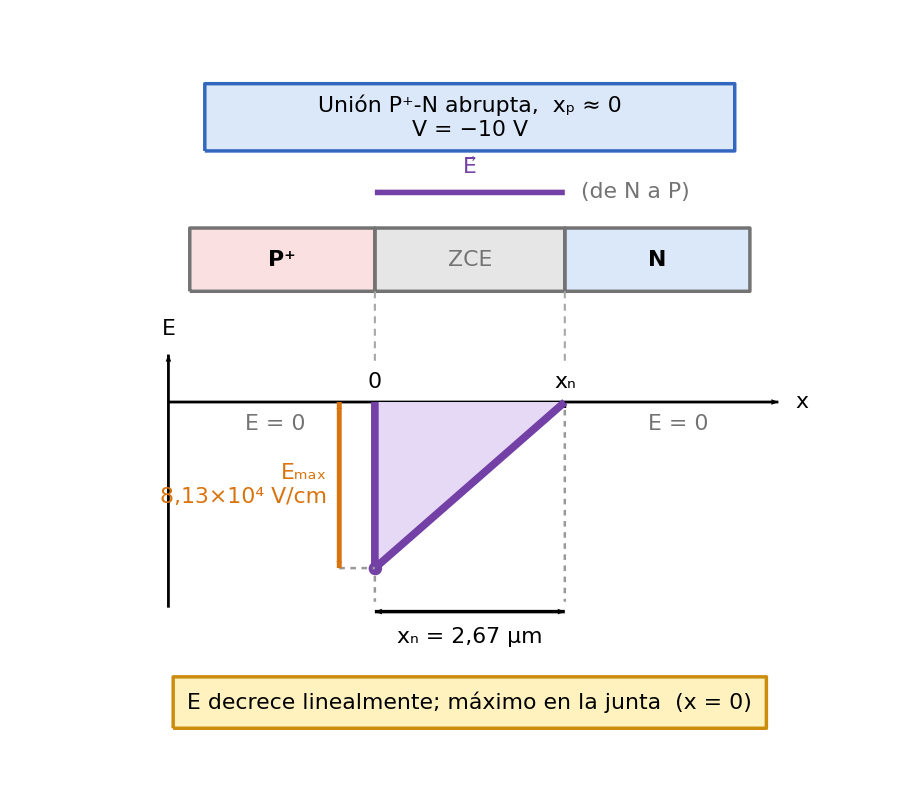

-Graphics-

```mathematica
{diagramaP6a, diagramaP7a} = Module[
  {fs, mostrarValores, cAzul, cAzulB, cRojoF, cVio, cVioF, cNar, cGris, cOro, cOroB,
   e, eps, NDc, VB, Vap, xn, Emax, xnum, sxu, cx0, X, yb, hE,
   ni, ND7, tau, mu, kT, Aar, V0, Dp, Lp, pn0, I0, I0p, Rd, Cd,
   ins, insI, insD, flecha, caja, dec, cient, xr, xc, yT, yB, g1, g2},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta los valores numéricos calculados *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojoF = RGBColor[0.98, 0.88, 0.88];
  cVio  = RGBColor[0.45, 0.25, 0.65];  cVioF  = RGBColor[0.90, 0.85, 0.96];
  cNar  = RGBColor[0.85, 0.45, 0.05];  cGris  = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del problema 6 (cm, V, F/cm) ---------- *)
  e = 1.6*10.^-19;  eps = 1.05*10.^-12;  NDc = 2.*10.^15;  VB = 0.85;  Vap = -10.;
  xn = Sqrt[2 eps (VB - Vap)/(e NDc)];     (* anchura de la ZCE (cm) *)
  Emax = e NDc xn/eps;                     (* campo máximo (V/cm) *)
  xnum = xn 10.^4;                         (* en micras *)

  (* ---------- Datos del problema 7 (cm, s, A) ---------- *)
  ni = 1.5*10.^10;  ND7 = 1.*10.^16;  tau = 1.*10.^-6;  mu = 450.;  kT = 0.026;
  Aar = 1.*10.^-3;  V0 = 0.60;
  Dp = kT mu;  Lp = Sqrt[Dp tau];  pn0 = ni^2/ND7;
  I0 = e Dp pn0/Lp Aar;  I0p = I0 Exp[V0/kT];
  Rd = kT/I0p;  Cd = I0p tau/(2 kT);

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.025], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  dec[x_, k_] := NumberForm[x, {5, k}, NumberPoint -> ","];
  cient[x_] := Module[{ex = Floor[Log10[x] + 10.^-9], m},
    m = Round[x/10.^ex, 0.01];
    Row[{If[m == Round[m], Round[m], NumberForm[m, {3, 2}, NumberPoint -> ","]],
      "×", Superscript["10", ex]}]];

  (* ===== Figura T4_P6_a: campo eléctrico en la ZCE de una unión P+-N ===== *)
  sxu = 1.8;  cx0 = 8.2;  yb = 8.6;  hE = 4.2;     (* escala horizontal (por micra), origen, base de E y altura de E_max *)
  X[u_] := cx0 + sxu u;
  g1 = Graphics[{
     (* cabecera *)
     caja[{10.6, 15.8}, {13.4, 1.7}, cAzul, cAzulB],
     ins[Column[{
        Row[{"Unión ", Superscript["P", "+"], "-N abrupta,  ", Subscript["x", "p"],
          " ≈ 0"}],
        If[mostrarValores,
         Row[{Style["V", Italic], " = −", Round[Abs[Vap]], " V"}],
         "polarización inversa"]}, Center], {10.6, 15.8}],

     (* esquema de la unión: P+ | ZCE | N *)
     {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cGris}],
      Rectangle[{X[-2.6], 11.4}, {X[0], 13.0}]},
     {GrayLevel[0.9], EdgeForm[{AbsoluteThickness[2.5], cGris, AbsoluteDashing[{7, 5}]}],
      Rectangle[{X[0], 11.4}, {X[xnum], 13.0}]},
     {cAzul, EdgeForm[{AbsoluteThickness[2.5], cGris}],
      Rectangle[{X[xnum], 11.4}, {X[xnum + 2.6], 13.0}]},
     ins[Style[Row[{Superscript["P", "+"]}], Bold], {X[-1.3], 12.2}],
     ins["ZCE", {X[xnum/2], 12.2}, cGris],
     ins[Style["N", Bold], {X[xnum + 1.3], 12.2}],
     flecha[{X[xnum], 13.9}, {X[0], 13.9}, cVio],
     ins[Row[{OverVector["E"]}], {X[xnum/2], 14.55}, cVio],
     insI["(de N a P)", {X[xnum] + 0.4, 13.9}, cGris],

     (* guías hacia el gráfico de E(x) *)
     {GrayLevel[0.65], AbsoluteThickness[1.5], AbsoluteDashing[{5, 4}],
      Line[{{X[0], 11.4}, {X[0], yb + 0.95}}],
      Line[{{X[xnum], 11.4}, {X[xnum], yb + 0.95}}]},

     (* ejes *)
     {Black, AbsoluteThickness[2], Arrowheads[0.025],
      Arrow[{{X[-2.9], yb}, {X[xnum + 3.0], yb}}], Arrow[{{X[-2.9], 3.4}, {X[-2.9], 9.8}}]},
     ins[Style["x", Italic], {X[xnum + 3.0] + 0.6, yb}],
     ins[Style["E", Italic], {X[-2.9], 10.45}],
     ins["0", {X[0], yb + 0.5}],
     ins[Row[{Subscript["x", "n"]}], {X[xnum], yb + 0.5}],
     Table[{Black, AbsoluteThickness[2], Line[{{X[u], yb}, {X[u], yb - 0.15}}]},
      {u, {0, xnum}}],

     (* E(x): nulo en P+, salto a -E_max en x = 0 y decrecimiento lineal hasta x_n *)
     {cVioF, EdgeForm[None], Polygon[{{X[0], yb}, {X[0], yb - hE}, {X[xnum], yb}}]},
     {cVio, AbsoluteThickness[5.5], Line[{{X[0], yb}, {X[0], yb - hE}, {X[xnum], yb}}]},
     {cVio, Disk[{X[0], yb - hE}, 0.17]},
     ins[Row[{Style["E", Italic], " = 0"}], {X[-1.4], yb - 0.55}, cGris],
     ins[Row[{Style["E", Italic], " = 0"}], {X[xnum + 1.6], yb - 0.55}, cGris],

     (* cota de E_max *)
     {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
      Line[{{X[-0.5], yb - hE}, {X[0], yb - hE}}]},
     {cNar, AbsoluteThickness[3.5], Arrowheads[{-0.014, 0.014}],
      Arrow[{{X[-0.5], yb}, {X[-0.5], yb - hE}}]},
     insD[Column[{Subscript["E", "max"],
        If[mostrarValores, Row[{cient[Emax], " V/cm"}], ""]}, Right],
      {X[-0.5] - 0.3, yb - hE/2}, cNar],

     (* cota de x_n *)
     {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
      Line[{{X[0], yb - hE - 0.2}, {X[0], 3.55}}],
      Line[{{X[xnum], yb - 0.2}, {X[xnum], 3.55}}]},
     {Black, AbsoluteThickness[2.5], Arrowheads[{-0.014, 0.014}],
      Arrow[{{X[0], 3.3}, {X[xnum], 3.3}}]},
     ins[Row[{Subscript["x", "n"],
        If[mostrarValores, Row[{" = ", dec[xnum, 2], " μm"}], ""]}],
      {X[xnum/2], 2.65}],

     (* nota *)
     caja[{10.6, 1.0}, {15.0, 1.3}, cOro, cOroB],
     ins[Row[{"E decrece linealmente; máximo en la junta  (", Style["x", Italic], " = 0)"}],
      {10.6, 1.0}]
    },
    ImageSize -> 900, PlotRange -> {{0.8, 19.4}, {0.2, 16.9}},
    PlotRangePadding -> None, AspectRatio -> 16.7/18.6, Background -> White];

  (* ===== Figura T4_P7_a: circuito equivalente de pequeña señal (R_d en paralelo con C_d) ===== *)
  xr = 6.5;  xc = 11.0;  yT = 9.0;  yB = 3.0;
  g2 = Graphics[{
     (* cabecera *)
     caja[{9.4, 12.0}, {14.4, 1.7}, cAzul, cAzulB],
     ins[Column[{"Modelo de pequeña señal",
        If[mostrarValores,
         Row[{"diodo ", Superscript["P", "+"], "-N en directa, ", Subscript["V", "0"],
           " = ", dec[V0, 2], " V"}],
         Row[{"diodo ", Superscript["P", "+"], "-N en directa"}]]}, Center], {9.4, 12.0}],

     (* carriles y terminales *)
     {Black, AbsoluteThickness[3.5],
      Line[{{2.5, yT}, {xc, yT}}], Line[{{2.5, yB}, {xc, yB}}]},
     {White, EdgeForm[{AbsoluteThickness[3], Black}],
      Disk[{2.5, yT}, 0.2], Disk[{2.5, yB}, 0.2]},
     ins[Superscript["P", "+"], {2.5, yT + 0.75}],
     ins["N", {2.5, yB - 0.75}],

     (* corriente y tensión de pequeña señal *)
     flecha[{3.2, yT + 0.65}, {5.2, yT + 0.65}, Black],
     ins[Style["i", Italic], {4.2, yT + 1.25}],
     flecha[{1.6, yB + 0.3}, {1.6, yT - 0.3}, Black],
     ins[Style["v", Italic], {0.95, 6.0}],

     (* resistencia de difusión R_d *)
     {cVio, AbsoluteThickness[4.5],
      Line[{{xr, yT}, {xr, 7.6}, {xr + 0.45, 7.3}, {xr - 0.45, 6.7}, {xr + 0.45, 6.1},
        {xr - 0.45, 5.5}, {xr + 0.45, 4.9}, {xr, 4.6}, {xr, yB}}]},
     insD[Column[{Subscript["R", "d"],
        If[mostrarValores, Row[{"≈ ", dec[Rd, 1], " Ω"}], ""]},
       Right], {xr - 0.8, 6.1}, cVio],
     ins[Column[{"resistencia", "de difusión"}, Center], {xr, 1.8}, cVio],

     (* capacidad de difusión C_d *)
     {cAzulB, AbsoluteThickness[4.5],
      Line[{{xc, yT}, {xc, 6.3}}], Line[{{xc - 0.95, 6.3}, {xc + 0.95, 6.3}}],
      Line[{{xc - 0.95, 5.7}, {xc + 0.95, 5.7}}], Line[{{xc, 5.7}, {xc, yB}}]},
     insI[Column[{Subscript["C", "d"],
        If[mostrarValores, Row[{"≈ ", dec[Cd 10.^9, 2], " nF"}], ""]},
       Left], {xc + 1.2, 6.0}, cAzulB],
     ins[Column[{"capacidad", "de difusión"}, Center], {xc, 1.8}, cAzulB],

     (* nodos *)
     {Black, Disk[{xr, yT}, 0.12], Disk[{xr, yB}, 0.12],
      Disk[{xc, yT}, 0.12], Disk[{xc, yB}, 0.12]},

     (* admitancia vista desde los terminales *)
     {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
      Line[{{xc, yT}, {15.2, yT}}], Line[{{xc, yB}, {15.2, yB}}]},
     {Black, AbsoluteThickness[2.5], Arrowheads[{-0.018, 0.018}],
      Arrow[{{15.2, yB}, {15.2, yT}}]},
     insI[Row[{"Y(", "ω", ")"}], {15.6, 6.0}],

     (* resumen *)
     caja[{9.4, 0.0}, {10.4, 1.2}, cOro, cOroB],
     ins[Row[{Subscript["R", "d"], " en paralelo con ", Subscript["C", "d"]}], {9.4, 0.0}]
    },
    ImageSize -> 900, PlotRange -> {{0.2, 18.4}, {-0.9, 13.2}},
    PlotRangePadding -> None, AspectRatio -> 14.1/18.2, Background -> White];

  {g1, g2}
];
diagramaP6a
diagramaP7a
```

```mathematica
Export[CloudObject["T4_P6_a.png"], diagramaP6a, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
Export[CloudObject["T4_P7_a.png"], diagramaP7a, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

-Graphics-

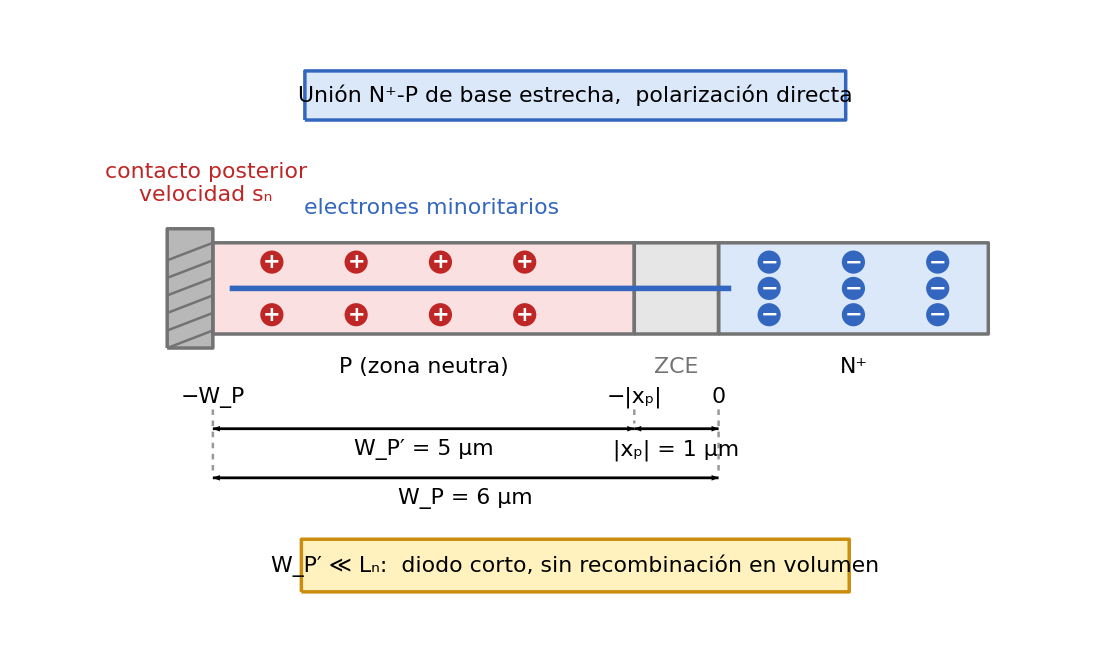

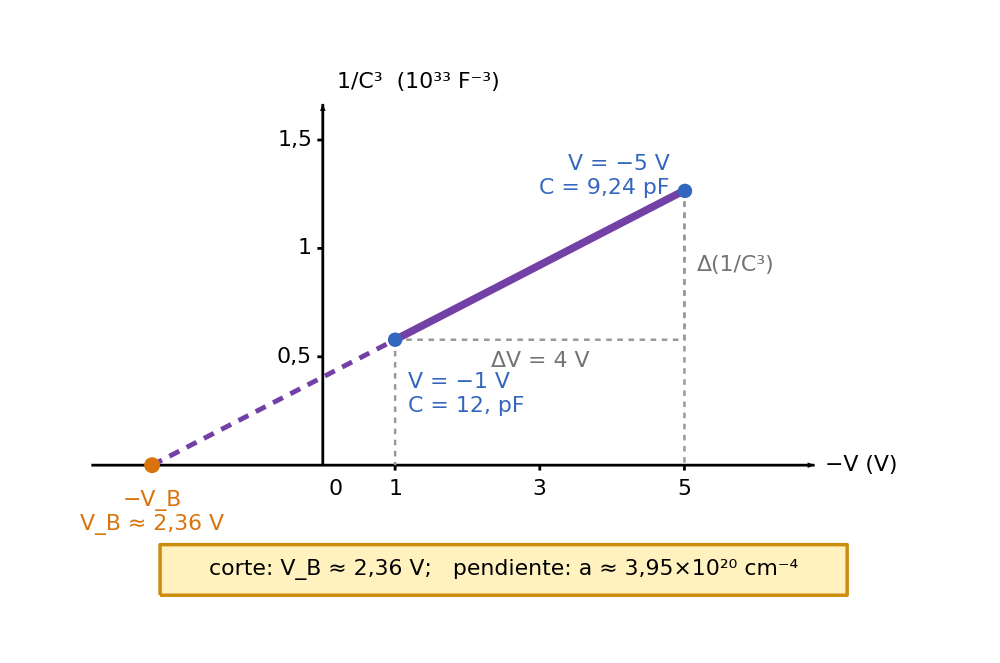

```mathematica
{diagramaP8a, diagramaP9a, diagramaP10a} = Module[
  {fs, mostrarValores, cAzul, cAzulB, cRojo, cRojoF, cVio, cNar, cGris, cOro, cOroB,
   e, G0, Aar, WN, xnu, Wp, JL, IL, sc, ox, X, y0p, hp, ff, pts, mT, ut,
   sc9, ox9, X9, WPu, xpu, WPp,
   eps10, A10, Vm, Cm, iC, xm, Kk, x0, VB10, a10, oxx, oyy, sxx, syy, XP, YP, y1, y2,
   ins, insI, insD, flecha, caja, carga, cotaH, onda, dec, cient, g1, g2, g3},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta los valores numéricos calculados *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo = RGBColor[0.75, 0.15, 0.15];  cRojoF = RGBColor[0.98, 0.88, 0.88];
  cVio  = RGBColor[0.45, 0.25, 0.65];  cNar   = RGBColor[0.85, 0.45, 0.05];
  cGris = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_, s_: 0.022] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  carga[pos_, signo_, col_] :=
    {col, Disk[pos, 0.33], Text[Style[signo, Round[0.95 fs], Bold, White], pos]};
  cotaH[xa_, xb_, y_] :=
    {Black, AbsoluteThickness[2], Arrowheads[{-0.020, 0.020}], Arrow[{{xa, y}, {xb, y}}]};
  onda[p1_, p2_, amp_, ciclos_] := Module[{d = p2 - p1, nv},
    nv = {-d[[2]], d[[1]]}/Norm[d];
    Table[p1 + s d + amp Sin[2 Pi ciclos s] nv, {s, 0., 1., 0.01}]];
  dec[x_, k_] := NumberForm[x, {5, k}, NumberPoint -> ","];
  cient[x_] := Module[{ex = Floor[Log10[x] + 10.^-9], m},
    m = Round[x/10.^ex, 0.01];
    Row[{If[m == Round[m], Round[m], NumberForm[m, {3, 2}, NumberPoint -> ","]],
      "×", Superscript["10", ex]}]];

  (* ===== Figura T4_P8_a: fotodiodo P+-N de base corta ===== *)
  e = 1.6*10.^-19;  G0 = 1.*10.^21;  Aar = 1.*10.^-4;
  WN = 4.;  xnu = 1.;  Wp = WN - xnu;                    (* micras *)
  JL = e G0 (Wp 10.^-4)/2;  IL = JL Aar;                  (* A/cm^2 y A *)
  sc = 2.6;  ox = 5.0;  X[u_] := ox + sc u;               (* u en micras, con u = 0 en la unión *)
  y0p = 6.2;  hp = 3.4;
  ff[u_] := (u - xnu) (WN - u)/(Wp/2)^2;                  (* perfil parabólico normalizado *)
  pts = Table[{X[u], y0p + hp ff[u]}, {u, xnu, WN, 0.05}];
  mT = hp 4/Wp;  ut = 0.6;                                (* pendiente en x_n y longitud de la tangente *)
  g1 = Graphics[{
     (* cabecera *)
     caja[{X[1.3], 19.7}, {13.8, 1.4}, cAzul, cAzulB],
     ins[Row[{"Fotodiodo ", Superscript["P", "+"], "-N de base corta,  polarización inversa"}],
      {X[1.3], 19.7}],

     (* luz: generación uniforme en la región neutra *)
     Table[{cNar, AbsoluteThickness[4], Arrowheads[0.02],
       Arrow[onda[{X[u], 17.0}, {X[u], 13.5}, 0.15, 3]]}, {u, {1.5, 2.5, 3.5}}],
     ins[Row[{"luz:  generación uniforme ", Subscript["G", "0"]}], {X[2.5], 17.9}, cNar],

     (* regiones: P+, ZCE, neutra N y contacto óhmico *)
     {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cGris}], Rectangle[{X[-1.8], 10.0}, {X[0], 13.2}]},
     {GrayLevel[0.9], EdgeForm[{AbsoluteThickness[2.5], cGris, AbsoluteDashing[{7, 5}]}],
      Rectangle[{X[0], 10.0}, {X[xnu], 13.2}]},
     {cAzul, EdgeForm[{AbsoluteThickness[2.5], cGris}], Rectangle[{X[xnu], 10.0}, {X[WN], 13.2}]},
     {cOro, EdgeForm[{AbsoluteThickness[2.5], cOroB}], Rectangle[{X[WN], 10.0}, {X[WN] + 0.5, 13.2}]},
     ins[Style[Row[{Superscript["P", "+"]}], Bold], {X[-0.9], 12.6}],
     ins["ZCE", {X[xnu/2], 12.6}, cGris],
     ins["región neutra N", {X[(xnu + WN)/2], 12.6}],
     insI[Column[{"contacto", "óhmico"}, Left], {X[WN] + 0.8, 11.6}, cOroB],

     (* reparto de los huecos fotogenerados: mitad recolectada, mitad perdida *)
     flecha[{X[2.5], 11.5}, {X[-0.5], 11.5}, cRojo],
     flecha[{X[2.5], 11.5}, {X[3.8], 11.5}, GrayLevel[0.5]],
     ins["recolectado 50 %", {X[1.9], 10.5}, cRojo],
     ins["perdido 50 %", {X[3.3], 10.5}, GrayLevel[0.4]],

     (* guías hacia el perfil *)
     Table[{GrayLevel[0.65], AbsoluteThickness[1.5], AbsoluteDashing[{5, 4}],
       Line[{{X[u], 10.0}, {X[u], y0p}}]}, {u, {0, xnu, WN}}],

     (* perfil parabólico del exceso de huecos *)
     {Opacity[0.2, cRojo], EdgeForm[None],
      Polygon[Join[pts, {{X[WN], y0p}, {X[xnu], y0p}}]]},
     {Black, AbsoluteThickness[2], Arrowheads[0.02],
      Arrow[{{X[-1.8], y0p}, {X[WN] + 1.6, y0p}}], Arrow[{{X[-1.8], y0p}, {X[-1.8], 9.1}}]},
     ins[Style["x", Italic], {X[WN] + 2.2, y0p}],
     ins[Row[{"δ", Subscript["p", "n"], "(", Style["x", Italic], ")"}], {X[-1.8], 9.65}],
     {cRojo, AbsoluteThickness[5.5], Line[pts]},
     {cRojo, Disk[{X[xnu], y0p}, 0.17], Disk[{X[WN], y0p}, 0.17]},

     (* pendiente en x_n: corriente recolectada *)
     {cNar, AbsoluteThickness[3.5], AbsoluteDashing[{8, 5}],
      Line[{{X[xnu], y0p}, {X[xnu + ut], y0p + mT ut}}]},
     insD[Row[{Subscript["J", "L"]}], {X[xnu] - 0.3, 7.7}, cNar],

     (* marcas del eje x y cotas *)
     Table[{Black, AbsoluteThickness[2], Line[{{X[u], y0p}, {X[u], y0p - 0.15}}]},
      {u, {0, xnu, WN}}],
     ins["0", {X[0], 5.65}],
     ins[Row[{Subscript["x", "n"]}], {X[xnu], 5.65}],
     ins[Row[{Subscript["W", "N"]}], {X[WN], 5.65}],
     {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
      Line[{{X[0], 5.3}, {X[0], 3.5}}], Line[{{X[xnu], 5.3}, {X[xnu], 4.95}}],
      Line[{{X[WN], 5.3}, {X[WN], 3.5}}]},
     cotaH[X[0], X[xnu], 4.8], cotaH[X[xnu], X[WN], 4.8], cotaH[X[0], X[WN], 3.3],
     ins[Row[{Subscript["x", "n"], " = ", Round[xnu], " μm"}], {X[xnu/2], 4.2}],
     ins[Row[{Subscript["W", "N"], "′ = ", Round[Wp], " μm"}],
      {X[(xnu + WN)/2], 4.2}],
     ins[Row[{Subscript["W", "N"], " = ", Round[WN], " μm"}], {X[WN/2], 2.7}],

     (* resultado *)
     caja[{X[1.3], 0.95}, {15.8, 1.5}, cOro, cOroB],
     ins[Row[{Subscript["J", "L"], " recolectada",
        If[mostrarValores,
         Row[{" ≈ ", dec[JL 1000, 1], " mA/", Superscript["cm", 2], ",   ",
           Subscript["I", "L"], " ≈ ", dec[IL 10.^6, 2], " μA"}], ""]}],
      {X[1.3], 0.95}]
    },
    ImageSize -> 1000, PlotRange -> {{-0.2, 19.2}, {0.1, 20.6}},
    PlotRangePadding -> None, AspectRatio -> 20.5/19.4, Background -> White];

  (* ===== Figura T4_P9_a: unión N+-P con recombinación superficial posterior ===== *)
  sc9 = 2.4;  ox9 = 17.2;  X9[u_] := ox9 + sc9 u;
  WPu = 6.;  xpu = 1.;  WPp = WPu - xpu;                  (* micras *)
  g2 = Graphics[{
     (* cabecera *)
     caja[{X9[-1.7], 14.8}, {15.4, 1.4}, cAzul, cAzulB],
     ins[Row[{"Unión ", Superscript["N", "+"], "-P de base estrecha,  polarización directa"}],
      {X9[-1.7], 14.8}],

     (* regiones: P neutra, ZCE y N+ *)
     {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cGris}], Rectangle[{X9[-WPu], 8.0}, {X9[-xpu], 10.6}]},
     {GrayLevel[0.9], EdgeForm[{AbsoluteThickness[2.5], cGris, AbsoluteDashing[{7, 5}]}],
      Rectangle[{X9[-xpu], 8.0}, {X9[0], 10.6}]},
     {cAzul, EdgeForm[{AbsoluteThickness[2.5], cGris}], Rectangle[{X9[0], 8.0}, {X9[3.2], 10.6}]},

     (* contacto posterior con recombinación superficial *)
     {GrayLevel[0.72], EdgeForm[{AbsoluteThickness[2.5], cGris}],
      Rectangle[{X9[-WPu] - 1.3, 7.6}, {X9[-WPu], 11.0}]},
     Table[{cGris, AbsoluteThickness[1.8], Line[{{X9[-WPu] - 1.3, y}, {X9[-WPu], y + 0.5}}]},
      {y, 7.6, 10.5, 0.5}],
     ins[Column[{"contacto posterior", Row[{"velocidad ", Subscript["s", "n"]}]}, Center],
      {X9[-WPu] - 0.2, 12.3}, cRojo],

     (* portadores: huecos en P, electrones en N+ *)
     Table[carga[{X9[u], y}, "+", cRojo], {u, {-5.3, -4.3, -3.3, -2.3}}, {y, {8.55, 10.05}}],
     Table[carga[{X9[u], y}, "−", cAzulB], {u, {0.6, 1.6, 2.6}}, {y, {8.55, 9.3, 10.05}}],

     (* difusión de electrones minoritarios hacia el contacto *)
     flecha[{X9[0.15], 9.3}, {X9[-5.8], 9.3}, cAzulB],
     ins["electrones minoritarios", {X9[-3.4], 11.6}, cAzulB],

     (* nombres de las regiones *)
     ins["P (zona neutra)", {X9[-3.5], 7.05}],
     ins["ZCE", {X9[-0.5], 7.05}, cGris],
     ins[Row[{Superscript["N", "+"]}], {X9[1.6], 7.05}],

     (* marcas de posición y cotas *)
     ins[Row[{"−", Subscript["W", "P"]}], {X9[-WPu], 6.2}],
     ins[Row[{"−|", Subscript["x", "p"], "|"}], {X9[-xpu], 6.2}],
     ins["0", {X9[0], 6.2}],
     {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
      Line[{{X9[-WPu], 5.85}, {X9[-WPu], 4.05}}], Line[{{X9[-xpu], 5.85}, {X9[-xpu], 5.45}}],
      Line[{{X9[0], 5.85}, {X9[0], 4.05}}]},
     cotaH[X9[-WPu], X9[-xpu], 5.3], cotaH[X9[-xpu], X9[0], 5.3], cotaH[X9[-WPu], X9[0], 3.9],
     ins[Row[{Subscript["W", "P"], "′ = ", Round[WPp], " μm"}], {X9[-3.5], 4.7}],
     ins[Row[{"|", Subscript["x", "p"], "| = ", Round[xpu], " μm"}], {X9[-0.5], 4.7}],
     ins[Row[{Subscript["W", "P"], " = ", Round[WPu], " μm"}], {X9[-3.], 3.3}],

     (* nota *)
     caja[{X9[-1.7], 1.4}, {15.6, 1.5}, cOro, cOroB],
     ins[Row[{Subscript["W", "P"], "′ ≪ ", Subscript["L", "n"],
        ":  diodo corto, sin recombinación en volumen"}], {X9[-1.7], 1.4}]
    },
    ImageSize -> 1100, PlotRange -> {{-0.4, 25.2}, {0.4, 15.8}},
    PlotRangePadding -> None, AspectRatio -> 15.4/25.6, Background -> White];

  (* ===== Figura T4_P10_a: 1/C^3 frente a -V en una unión gradual lineal ===== *)
  eps10 = 1.05*10.^-12;  A10 = 1.*10.^-3;
  Vm = {-1., -5.};  Cm = {12., 9.24};                    (* V y pF *)
  iC = 1/(Cm 10.^-12)^3;                                  (* 1/C^3 en F^-3 *)
  xm = -Vm;                                               (* tensión inversa -V *)
  Kk = (iC[[2]] - iC[[1]])/(xm[[2]] - xm[[1]]);           (* pendiente respecto a -V *)
  x0 = xm[[1]] - iC[[1]]/Kk;  VB10 = -x0;                 (* corte con el eje: -V_B *)
  a10 = 12/(A10^3 e eps10^2 Kk);                          (* gradiente de dopado (cm^-4) *)
  y1 = iC[[1]]/10.^33;  y2 = iC[[2]]/10.^33;
  oxx = 6.4;  oyy = 3.6;  sxx = 2.0;  syy = 6.0;
  XP[v_] := oxx + sxx v;  YP[y_] := oyy + syy y;          (* v = -V (V),  y = 1/C^3 en 10^33 F^-3 *)
  g3 = Graphics[{
     (* ejes y marcas *)
     {Black, AbsoluteThickness[2], Arrowheads[0.02],
      Arrow[{{XP[-3.2], oyy}, {XP[6.8], oyy}}], Arrow[{{XP[0], oyy}, {XP[0], 13.6}}]},
     ins[Row[{"−", Style["V", Italic], " (V)"}], {XP[6.8] + 1.3, oyy}],
     insI[Row[{"1/", Superscript[Style["C", Italic], 3], "  (", Superscript["10", 33], " ",
        Superscript["F", "−3"], ")"}], {XP[0] + 0.4, 14.2}],
     Table[{Black, AbsoluteThickness[2], Line[{{XP[v], oyy}, {XP[v], oyy - 0.15}}],
       ins[ToString[v], {XP[v], oyy - 0.65}]}, {v, {1, 3, 5}}],
     ins["0", {XP[0] + 0.35, oyy - 0.65}],
     Table[{Black, AbsoluteThickness[2],
       Line[{{XP[0] - 0.15, YP[t[[1]]]}, {XP[0], YP[t[[1]]]}}],
       insD[t[[2]], {XP[0] - 0.3, YP[t[[1]]]}]}, {t, {{0.5, "0,5"}, {1., "1"}, {1.5, "1,5"}}}],

     (* guías, triángulo de la pendiente y puntos medidos *)
     {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
      Line[{{XP[xm[[1]]], YP[y1]}, {XP[xm[[1]]], oyy}}],
      Line[{{XP[xm[[2]]], YP[y2]}, {XP[xm[[2]]], oyy}}],
      Line[{{XP[xm[[1]]], YP[y1]}, {XP[xm[[2]]], YP[y1]}, {XP[xm[[2]]], YP[y2]}}]},
     ins[Row[{"Δ", Style["V", Italic], " = ", Round[xm[[2]] - xm[[1]]], " V"}],
      {XP[(xm[[1]] + xm[[2]])/2], YP[y1] - 0.6}, cGris],
     insI[Row[{"Δ(1/", Superscript[Style["C", Italic], 3], ")"}],
      {XP[xm[[2]]] + 0.35, (YP[y1] + YP[y2])/2}, cGris],

     (* recta: extrapolación (discontinua) y tramo medido (continuo) *)
     {cVio, AbsoluteThickness[3.5], AbsoluteDashing[{8, 6}],
      Line[{{XP[x0], oyy}, {XP[xm[[1]]], YP[y1]}}]},
     {cVio, AbsoluteThickness[5.5], Line[{{XP[xm[[1]]], YP[y1]}, {XP[xm[[2]]], YP[y2]}}]},
     {cAzulB, Disk[{XP[xm[[1]]], YP[y1]}, 0.2], Disk[{XP[xm[[2]]], YP[y2]}, 0.2]},
     insI[Column[{Row[{Style["V", Italic], " = −", Round[-Vm[[1]]], " V"}],
        Row[{Style["C", Italic], " = ", dec[Cm[[1]], 0], " pF"}]}, Left],
      {XP[xm[[1]]] + 0.35, YP[y1] - 1.5}, cAzulB],
     insD[Column[{Row[{Style["V", Italic], " = −", Round[-Vm[[2]]], " V"}],
        Row[{Style["C", Italic], " = ", dec[Cm[[2]], 2], " pF"}]}, Right],
      {XP[xm[[2]]] - 0.4, YP[y2] + 0.4}, cAzulB],

     (* corte con el eje: -V_B *)
     {cNar, Disk[{XP[x0], oyy}, 0.22]},
     ins[Column[{Row[{"−", Subscript["V", "B"]}],
        If[mostrarValores, Row[{Subscript["V", "B"], " ≈ ", dec[VB10, 2], " V"}], ""]},
       Center], {XP[x0], oyy - 1.3}, cNar],

     (* resultado *)
     caja[{11.4, 0.7}, {19.0, 1.4}, cOro, cOroB],
     ins[Row[{"corte: ", Subscript["V", "B"],
        If[mostrarValores, Row[{" ≈ ", dec[VB10, 2], " V"}], ""],
        ";   pendiente: ", Style["a", Italic],
        If[mostrarValores,
         Row[{" ≈ ", cient[a10], " ", Superscript["cm", "−4"]}], ""]}],
      {11.4, 0.7}]
    },
    ImageSize -> 1000, PlotRange -> {{0., 22.6}, {-0.2, 14.8}},
    PlotRangePadding -> None, AspectRatio -> 15./22.6, Background -> White];

  {g1, g2, g3}
];
diagramaP8a
diagramaP9a
diagramaP10a
```

```mathematica
Export[CloudObject["T4_P8_a"], diagramaP8a,"PNG", Background -> None, ImageResolution -> 300, ImageSize -> 1000]
Export[CloudObject["T4_P9_a"], diagramaP9a,"PNG", Background -> None, ImageResolution -> 300, ImageSize -> 1100]
Export[CloudObject["T4_P10_a"], diagramaP10a,"PNG", Background -> None, ImageResolution -> 300, ImageSize -> 1000]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_P8_a]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_P9_a]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_P10_a]